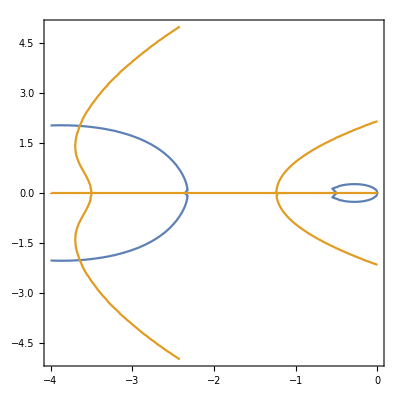

General::ivar: a+ⅈ b is not a valid variable.

```mathematica
δ=(vr^2-vt^2+2 μ (vt-vr))/(4 d);

PL=Exp[δ] ParabolicCylinderD[-s,(μ-vr)/Sqrt[d]]/ParabolicCylinderD[-s,(μ-vt)/Sqrt[d]];

param={μ->0.8,vr->0,vt->1,d->0.1};

Pplot=Exp[δ] ParabolicCylinderD[-s,(μ-vr)/Sqrt[d]]/ParabolicCylinderD[-s,(μ-vt)/Sqrt[d]]/.param;
s=a+I*b;
ContourPlot[{Re[Pplot]==1,Im[Pplot]==0,0},{a,-4,0},{b,-5,5}]


Finv=s/(PL);
g=Normal[Simplify[Series[Finv,{s,0,1}]]];
```